```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
a=.998`32;
r0 = 10`32;
x = Cos[π/4`32];
Freqs=KerrGeoFrequencies[a,r0,0,x];
Ωθ=Freqs[[2]];
Ωϕ= Freqs[[3]];
orbit = KerrGeoOrbit[a,r0,0,x];
{t,r,θ,ϕ} = orbit["Trajectory"];
Υ = orbit["Frequencies"]["Υ_θ"];
Υϕ = orbit["Frequencies"]["Υ_ϕ"];
ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
```

```mathematica
l=3;
m=-1;
knum = 20;

dtdλ[θ_]:= ℰ(((r0^2+a^2)^2)/(r0^2-2 r0+a^2)-a^2 Sin[θ]^2)+a ℒ(1-(r0^2+a^2)/(r0^2-2r0 +a^2))


ut[θ_]:=-(4 a r0 ℒ)/((a^2+(-2+r0) r0) (a^2+2 r0^2+a^2 Cos[2 θ]))+(ℰ (a^4+2 r0^4+a^2 r0 (2+3 r0)+a^2 (a^2+(-2+r0) r0) Cos[2 θ]))/((a^2+(-2+r0) r0) (a^2+2 r0^2+a^2 Cos[2 θ]))

S = Table[SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ+k Ωθ)],{l,0,5},{m,-l,l},{k,-knum,knum}];
```

```mathematica
T = -(2 Ωθ r0)/(r0^2-2 r0 +a^2)Table[NIntegrate[(S[[l+1,l+m+1,1+knum+k]][θ[λ],0])/ut[θ[λ]] Cos[m(Ωϕ t[λ]-ϕ[λ])+k Ωθ t[λ]]dtdλ[λ],{λ,0,(2π)/Υ},(*Method->"Trapezoidal",*)PrecisionGoal->10],{k,-knum,knum}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {1.7866410503574976062693122208637841810685564780669665196910500526}. NIntegrate obtained 0.0000244257 and 2.12355×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {1.7866410523568355187250876309417271011609207320702807919587939978}. NIntegrate obtained 0.0000272075 and 6.09448×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {3.20437×10^-8}. NIntegrate obtained 0.0000304931 and 1.86089×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

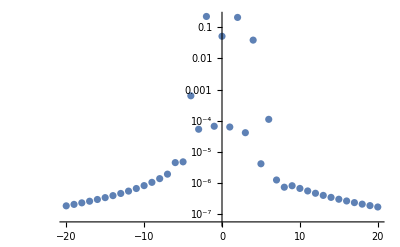

```mathematica
ListLogPlot[Thread[{Table[k,{k,-knum,knum}],Abs[T]}]]
```

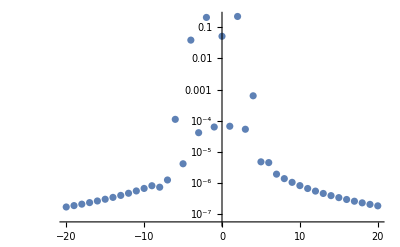

-Graphics-